```mathematica
SetDirectory[NotebookDirectory[]]
<<MaTeX`
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö

```mathematica
hepData=Import["HEP_phenix/Table1.csv"];
pT1=hepData[[All,1]];
σ1=hepData[[All,4]];
hep=Transpose[{pT1,σ1}];
```

```mathematica
pythiaData=Import["Pythia/Tests/pT cross section/pT.csv"];
{pT2,σ2}=Transpose[{#1,Around[#2,#3]}&@@@pythiaData];
pythia=Transpose[{pT2,σ2}];
```

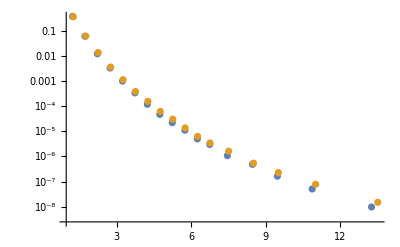

```mathematica
ListLogPlot[{hep,pythia},PlotRange->All,IntervalMarkers->None]
```

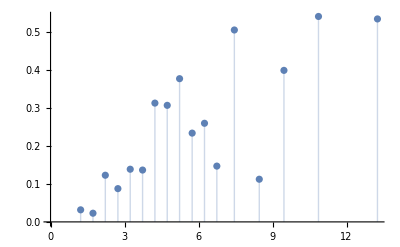

```mathematica
ListPlot[Transpose[{pT1,Abs[σ1-σ2]/σ1}],Filling->Axis,IntervalMarkers->None]
```